```mathematica
set1Mode1 = Drop[Import[FileNameJoin[{NotebookDirectory[],"out1_p096_sudoku.txt"} ], "Data"], 1];
set1Mode2= Drop[Import[FileNameJoin[{NotebookDirectory[],"out2_p096_sudoku.txt"} ], "Data"], 1];
set2Mode1= Drop[Import[FileNameJoin[{NotebookDirectory[],"out1_su17ExtremeDiff500.txt"} ], "Data"], 1];
```

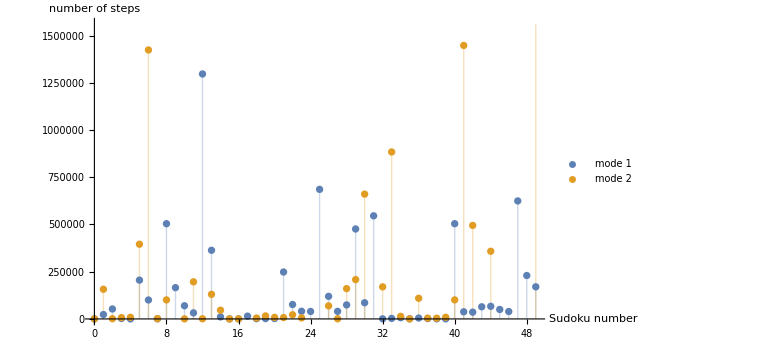

```mathematica
stepsplot1= Table[{set1Mode1[[i]][[1]], set1Mode1[[i]][[2]]},{i,1, Length[set1Mode1]}];
stepsplot2= Table[{set1Mode2[[i]][[1]], set1Mode2[[i]][[2]]},{i,1, Length[set1Mode2]}];
ListPlot[{stepsplot1,stepsplot2}, Filling->Axis, PlotLegends->{"mode 1", "mode 2"}, AxesLabel->{"Sudoku number", "number of steps"},ImageSize->Large]
Export[ FileNameJoin[{NotebookDirectory[],"steps.pdf"} ],%];
```

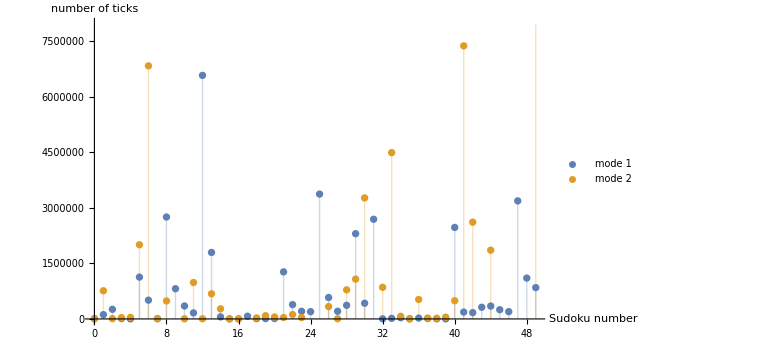

```mathematica
ticksplot1= Table[{set1Mode1[[i]][[1]], set1Mode1[[i]][[4]]},{i,1, Length[set1Mode1]}];
ticksplot2= Table[{set1Mode2[[i]][[1]], set1Mode2[[i]][[4]]},{i,1, Length[set1Mode2]}];
ListPlot[{ticksplot1,ticksplot2}, Filling->Axis, PlotLegends->{"mode 1", "mode 2"}, AxesLabel->{"Sudoku number", "number of ticks"},ImageSize->Large]
Export[ FileNameJoin[{NotebookDirectory[],"ticks.pdf"} ],%];
```

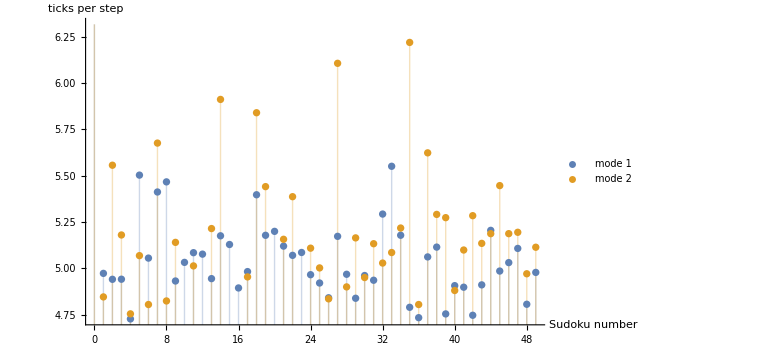

```mathematica
ticksperstep1= Table[{set1Mode1[[i]][[1]], set1Mode1[[i]][[4]]/set1Mode1[[i]][[2]]},{i,1, Length[set1Mode1]}];
ticksperstep2= Table[{set1Mode2[[i]][[1]], set1Mode2[[i]][[4]]/set1Mode2[[i]][[2]]},{i,1, Length[set1Mode2]}];
ListPlot[{ticksperstep1,ticksperstep2}, Filling->Axis, PlotLegends->{"mode 1", "mode 2"}, AxesLabel->{"Sudoku number", "ticks per step"},ImageSize->Large]
Export[ FileNameJoin[{NotebookDirectory[],"ticksperstep.pdf"} ],%];
```

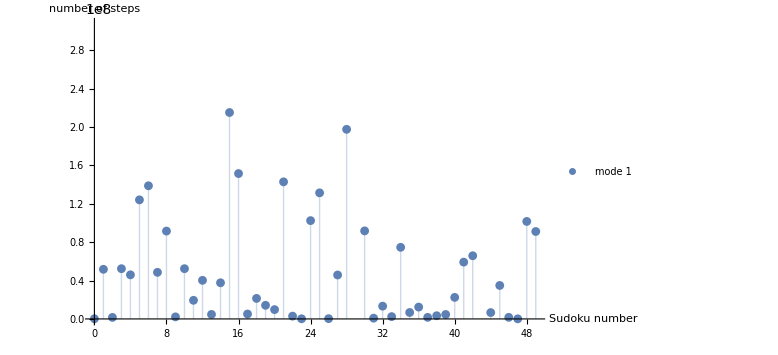

```mathematica
stepsplot21= Table[{set2Mode1[[i]][[1]], set2Mode1[[i]][[2]]},{i,1, Length[set2Mode1]}];
(*stepsplot22= Table[{set2Mode2[[i]][[1]], set2Mode2[[i]][[2]]},{i,1, Length[set2Mode2]}];*)
ListPlot[{stepsplot21}, Filling->Axis, PlotLegends->{"mode 1", "mode 2"}, AxesLabel->{"Sudoku number", "number of steps"},ImageSize->Large]
Export[ FileNameJoin[{NotebookDirectory[],"steps2.pdf"} ],%];
```

```mathematica
steps1= Table[set1Mode1[[i]][[2]],{i,1, Length[set1Mode1]}];
steps2= Table[set1Mode2[[i]][[2]],{i,1, Length[set1Mode2]}];
ticks1= Table[set1Mode1[[i]][[4]],{i,1, Length[set1Mode1]}];
ticks2= Table[set1Mode2[[i]][[4]],{i,1, Length[set1Mode2]}];
ms1= Table[set1Mode1[[i]][[3]],{i,1, Length[set1Mode1]}];
ms2= Table[set1Mode2[[i]][[3]],{i,1, Length[set1Mode2]}];
```

```mathematica
Mean[steps1]//N
StandardDeviation[steps1]//N
```

142413.

246524.

```mathematica
Mean[ticks1]//N
StandardDeviation[ticks1]//N
```

716981.

1.24549×10^6

```mathematica
Mean[ms1]//N
StandardDeviation[ms1]//N
```

183.4

319.424

```mathematica
Mean[steps2]//N
StandardDeviation[steps2]//N
```

4.92213×10^6

1.82478×10^7

```mathematica
Mean[ticks2]//N
StandardDeviation[ticks2]//N
```

2.54179×10^7

9.39989×10^7

```mathematica
Mean[ms2]//N
StandardDeviation[ms2]//N
```

6518.32

24107.5

```mathematica
steps21= Table[set2Mode1[[i]][[2]],{i,1, Length[set2Mode1]}];
ticks21= Table[set2Mode1[[i]][[4]],{i,1, Length[set2Mode1]}];
ms21= Table[set2Mode1[[i]][[3]],{i,1, Length[set2Mode1]}];
```

```mathematica
Mean[steps21]//N
StandardDeviation[steps21]//N
```

7.31106×10^7

1.45538×10^8

```mathematica
Mean[ticks21]//N
StandardDeviation[ticks21]//N
```

3.3436×10^8

6.71783×10^8

```mathematica
Mean[ms21]//N
StandardDeviation[ms21]//N
```

85751.5

172290.

```mathematica
tps1 = ticks1/steps1//N
tps2 = ticks2/steps2//N
```

{4.74527,4.52079,4.68479,4.37355,4.48228,4.59076,4.54603,4.5367,4.29977,4.49361,4.49907,4.53446,4.37352,4.45984,4.52732,4.45194,4.58773,4.94928,4.65024,4.41664,4.67067,4.74767,4.47512,4.48171,4.61869,4.45691,4.646,4.48128,4.41885,4.66909,4.66548,4.44106,4.60925,4.41856,4.62399,4.43145,4.53559,4.6162,4.6658,4.75725,4.48608,4.70809,4.8394,4.62092,4.46517,4.51952,4.60227,4.22961,4.55116,4.50341}

{29.8581,4.84641,5.55655,5.1804,4.75512,5.06901,4.8054,5.67588,4.82465,5.14055,6.57416,5.01362,6.375,5.21497,5.9113,19.2,23.9906,4.95433,5.83954,5.4411,6.39019,5.15716,5.38687,6.60502,5.10927,5.0028,4.836,6.10604,4.90043,5.16472,4.95091,5.13328,5.02901,5.08577,5.21786,6.21866,4.80539,5.62324,5.29133,5.27379,4.88101,5.09929,5.28445,5.13515,5.18738,5.44661,5.18752,5.19492,4.97121,5.11429}

```mathematica
Mean[tps1]//N
StandardDeviation[tps1]//N
```

4.5536

0.134273

```mathematica
Mean[tps2]//N
StandardDeviation[tps2]//N
```

6.46033

4.71489